```mathematica
SetDirectory[NotebookDirectory[]];
mmax=2;
dispNumInt=7;
nullNumInt=5;
(*discretization steps and B,J cutoffs*)
δb=1/10;
Bmax=40;
nodenum=8;
(*x values with added points to fix functional negative regions*)
xs0=N[Join[{1/1000000000,1/100000000,1/1000000,101/2000000,1/10000,0.001,0.0055000000000000005,0.009,0.009099999999999999,0.0092,0.0093,0.0094,0.0095,0.0096,0.0097,0.0098,0.0099,0.01,0.043,0.0445,0.046,0.0475,0.049,0.05,0.05500000000000001,0.060000000000000005,0.065,0.07,0.07500000000000001,0.08000000000000002,0.085,0.09000000000000001,0.09500000000000001,0.1,0.10700000000000001,0.114,0.115,0.116,0.117,0.118,0.119,0.12,0.12100000000000001,0.128,0.135,0.14,0.15000000000000002,0.16,0.17,0.17200000000000001,0.17400000000000002,0.176,0.178,0.18,0.19,0.2,0.21,0.218,0.226,0.23399999999999999,0.242,0.25,0.3,0.31,0.32,0.32999999999999996,0.33999999999999997,0.34,0.34444444444444444,0.3488888888888889,0.35,0.35000000000000003,0.35333333333333333,0.3577777777777778,0.3622222222222222,0.3666666666666667,0.3711111111111111,0.37555555555555553,0.38,0.4,0.45,0.5,0.55,0.6000000000000001,0.6500000000000001,0.7000000000000001,0.7500000000000001,0.8,.815,0.831,0.83175,0.8325,0.8332499999999999,0.834,0.8500000000000001,0.9000000000000001,0.9500000000000001,.976,.99}]//Rationalize,50];

xs=N[Rationalize[Join[{0.2843640712034819,0.5328905973077236,0.339734749002208,0.767536534713478,0.9176793390547109,0.7159028829214302,0.9131635336820303},{0.2844977808672184,0.5325933765926307,0.34052769937747057,0.2834977808672184,0.5315933765926307,0.33952769937747057,0.2854977808672184,0.5335933765926307,0.3415276993774706},{0.9662385242891698,0.9791138448895915,0.9684633399702889,0.9779527622203725,0.9561107926746197,0.9428958616016427,0.20735373976892385,0.1585087544655452},{0.28485318996712583,0.537404810832206,0.7470303087499952,0.894571893761059,0.9132196086869063,0.9274380084615406,0.9384966642649997,0.9472486411068909},{1/1000000000,1/100000000,1/1000000,101/2000000,1/10000,0.001,0.0055000000000000005,0.009,0.009099999999999999,0.0092,0.0093,0.0094,0.0095,0.0096,0.0097,0.0098,0.0099,0.01,0.043,0.0445,0.046,0.0475,0.049,0.05,0.05500000000000001,0.060000000000000005,0.065,0.07,0.07500000000000001,0.08000000000000002,0.085,0.09000000000000001,0.09500000000000001,0.1,0.10700000000000001,0.114,0.115,0.116,0.117,0.118,0.119,0.12,0.12100000000000001,0.128,0.135,0.14,0.15000000000000002,0.16,0.17,0.17200000000000001,0.17400000000000002,0.176,0.178,0.18,0.19,0.2,0.21,0.218,0.226,0.23399999999999999,0.242,0.25,0.3,0.31,0.32,0.32999999999999996,0.33999999999999997,0.34,0.34444444444444444,0.3488888888888889,0.35,0.35000000000000003,0.35333333333333333,0.3577777777777778,0.3622222222222222,0.3666666666666667,0.3711111111111111,0.37555555555555553,0.38,0.4,0.45,0.5,0.55,0.6000000000000001,0.6500000000000001,0.7000000000000001,0.7500000000000001,0.8,.815,0.831,0.83175,0.8325,0.8332499999999999,0.834,0.8500000000000001,0.9000000000000001,0.9500000000000001,.976,.99},{0.4926411109490251728709606264411364889182908469970995636647366741332486541054074177940508042273651920,0.6240307789622636593664087777097140265628695487976074218750000000000000000000000000000000000000000000,0.7166266862755098226811369511421869112381417401123046875000000000000000000000000000000000000000000000,0.976986392704580743739435265439285842182378410116903022754564327680274620699989102764657918162578415,0.8991942701753934892673391432721140712123220114515277353523924809607508812688650503062364769582049028,0.9798588498829338441249058472166910349333266038489483543600877913546744554722646756632864543472334573,0.9115227510947062079522192873354890715370583861727979321771817351685175150351412613219358701404241962,0.9822525749338889492523534402769222437980439657673808029972405880727201020350245993948523886429449971,0.9218466158224367100906718318314203282615153684604357280151100204570047902012328693494810956423547235,0.9842627756285038723328713463305451690102527688003929957682765727304293548378030307102174645104987061,0.9305737891134204362852142108955017766551434269012637058819677191012684940491885880911831587892963462,0.985963556833395917758986659746471877305939015122668089609928260159628982081041026429123653770693712},{0.9065805416377608591175327199874558307338862728297040210414459007621363143951744699650300053172448554752846732071885`100.,0.9183303206633781207338675679268501603637847232066953432186131862479852467740693215748630740834904044768699020618504`100.,0.9280357692093975075255722968362349011257677536314455343182751716849402812306354955899626868863415291923208749287318`100.},{0.5224565711756487143727215162566628659847919854437915370126287913814677659290496531627017473748514585081464062206484`100.,0.6420689942453308972001830454701121198013424873352050781249999999999999999999999999999999999999999999999999999999999`100.,0.985340622698034971670227170303585975742377581587490555332236532845629936333256816142699192224552545449989296080481`100.,0.9339426852457027271725147022573735611738505246332764044387108362609176670804093310339679018070681731236078987212947`100.,0.9871006278593887999314917261615572458214750445018542255643974380254935970145166808881443101928522654608343732464865`100.},{0.9290675600250443768554794532662853523318543657207645260133740051547753039121802161042399883452715372327537876690774`100.},{0.294237661132469571109557112830764100959664933224506178576900507370151410899495378317356724947393413824114634782303678588262330915143861091993680144582227058609480090711755811432613224371589971579734975232959468701308696923760826617993727571250578435572645744345849388093220703440081476538625410662539929529946186559190083421415`300.,0.949389094444290981732204214207146663230784989601541263376860981924793766500242573122476122177709797443190556158961157875167458725328682178704290483159028613558512107616774354239321756172906633935523759582134919274711457478911223289910534229449402284476167915810850685672421270591438063192920808875660368869212017771488434606182`300.,0.954309013219973229828009524609148666303473731405303707269586134691859210024478676349312086670618870987252086321705618630078223673798282778256956030451991206936801489316463486314809922499646687442131531670208471715765331304849872445078223448926503523168637280222327810558202822378704930556719990901458909801235602566659584780765`300.,0.958536123601445537408437183938227748587280075859655743903984772920587202748189305147765795413215255732978642048909343902963795699170659295524253059407689421329411359942266323843742205156058911406931270991474978498632554462910805553087882561236985164646332823615899307489999561445380238646841266783420846725784279175673945502573`300.,0.962196300298551046414920502225144404605988164485513839700307081721771132242843452139430061531838908559364714677932162692901787077225419570526186268671787162942726765769950036910542483671140411114548100385047111178192900856127817701497756696630082677314177541907840128634676206951912279702661815167033621494647153996142735683237`300.,0.92530095987761167520752374271511978155023815908292096809865807916554355781459325306328694704854880338559769103583321589003351487751722197896856816364039740277941153506354842535478549225540290343000208640781570479893375837625227506242272190159846775124747382573721233509372529523943025794222961817591403696709538375224051168716`300.,0.002250522341347322844737256076823419803569515667177497417083193018551976359898337669289677520905041917912049005449663585699375668576355338468226238104384412416922058281486431885032894921380985167814947578477770210447908838825649930077902476186443869348755679977465058109487213044144694071053286735859555418975060112712856591307`300.},{0.28474683124444444,0.5366410921074699,0.9755569213495311,0.7401263339588746,0.7964407777724928},{0.2845003250106347,0.5326279134153455,0.34053746465868473,0.7676791083165428,0.8373836809364477,0.9216911264267935,0.2945003250106347,0.5426279134153456,0.35053746465868474,0.7776791083165429,0.8473836809364477,0.9316911264267935,0.2745003250106347,0.5226279134153455,0.3305374646586847,0.7576791083165428,0.8273836809364477,0.9116911264267935}],0],200];
```

```mathematica
fileFcVals="fcExpandVals.wdx";
integralsFileName="generalColorJ30m10.wdx";
```

```mathematica
inputs
```

```mathematica
not improved disperion relation
```

```mathematica
dispRelHighE[Mp_,W_]:=s (-s-t)P[J,1+2t/μ]/(μ+t)((W.Mp.W)/(μ-s)+(W.Mp)/(μ+s+t));
dispLowE[W_,R_]:=(s+t)/t B[0,t,R]-s/t W[R,R] B[0,t,R]-B[s,t,R]-8 Pi G/t KroneckerDelta[R,1] s (-s-t)
```

```mathematica
improved dispersion relation
```

```mathematica
CimpEvenR=1/((t-μ) μ^3 (t+μ)^2)(t (t-μ) (Mp (3 t^2+5 t μ+μ^2)-μ (t+μ) Mp.W) P[J,1]-(t-μ) μ^2 (Mp μ+(t+μ) Mp.W) P[J,1+(2 t)/μ]-2 t^2 (t+μ) (Mp (t-μ)+δ (t+μ)) Derivative[0,1][P][J,1]);

CimpOddR=1/((t-μ) μ^3 (t+μ)^2)(t (-2 δ μ (t+μ)^2+Mp (3 t^3+2 t^2 μ-4 t μ^2-μ^3)+(-t^2 μ+μ^3) Mp.W) P[J,1]+(t-μ) μ^2 (Mp μ+(t+μ) Mp.W) P[J,1+(2 t)/μ]-2 t^2 (t+μ) (Mp (t-μ)-δ (t+μ)) Derivative[0,1][P][J,1]);
CimpLowE=(8 G π Pt[1])/t+1/2 (Derivative[0,2][B][0,0]-Derivative[0,2][WB][0,0])-Derivative[1,1][B][0,0]-1/2 t Derivative[1,2][B][0,0];
```

```mathematica
MpSonAdj={{2/((-1+n) n),2/((-1+n) n),2/((-1+n) n),2/((-1+n) n),2/((-1+n) n),2/((-1+n) n)},{(2+n)/n,(-8+n^2)/(2 (-2+n) n),(-4+n)/((-2+n) n),-(2 (2+n))/((-2+n) n),(8+2 n-n^2)/(4 n-2 n^2),-4/((-2+n) n)},{(6+7 n-n^3)/(6-6 n),(12+5 n-6 n^2+n^3)/(6 (2-3 n+n^2)),(11-6 n+n^2)/(6-9 n+3 n^2),(2+3 n+n^2)/(6-9 n+3 n^2),(6+7 n-n^3)/(6 (2-3 n+n^2)),(4+3 n-n^2)/(6-9 n+3 n^2)},{1/12 (6-5 n+n^2),(3-n)/6,1/6,1/6,1/6 (-3+n),-1/6},{-1,-(-4+n)/(2 (-2+n)),1/(-2+n),-2/(-2+n),-1/2,0},{1/4 (6+n-n^2),(-3+n)/(-2+n),(-4+n)/(2 (-2+n)),(2+n)/(2 (-2+n)),0,-1/2}};
WSonAdj={{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,-1,0},{0,0,0,0,0,-1}};

MplusSO2={{1/2,1/2,1/2},{-1/2,-1/2,1/2},{1,-1,0}};
WSO2=DiagonalMatrix[{1,-1,1}];
```

```mathematica
<<"full_bounds_2sub_int_fwd.wl";
```

```mathematica
Explicity improved dispersion relation in Pt basis
```

```mathematica
getCimpLowE[MpSonAdj/.n->5,WSonAdj,CimpLowE]
```

{(8 G π)/t+14/3 g[2,1]-2/3 g[2,2]+g[2,3]-7 g[2,4]-1/2 t (-14 g[3,1]-16 g[3,2]-2 g[3,3]+14 g[3,4]),-1/3 g[2,1]-2/3 g[2,2]+g[2,3]-2 g[2,4]-1/2 t (6 g[3,1]-6 g[3,2]-2 g[3,3]+4 g[3,4]),-1/3 g[2,1]-2/3 g[2,2]-g[2,4]-t g[3,4],-7/3 g[2,1]+4/3 g[2,2]-g[2,3]-t g[3,3],-3 t g[3,2],-3 t g[3,1]}

```mathematica
(*Args: 
0. list of eft coupling rules, with g being the objective
1. list of eft coupling replacement rules, for redefining the couplings
2. not improved high E dispersion relation dispRelHighE[Mp,W]
3. not improved low E dispersion relation dispLowE[W,R]
4. improved high E symmetric rep dispersion relation, in terms of {t,μ,Mp,Mp.W,P[J,1],P[J,1+(2 t)/μ],δ,P^(0,1)[J,1]}
5. improved high E antisymmetric rep dispersion relation, in terms of {t,μ,Mp,Mp.W,P[J,1],P[J,1+(2 t)/μ],δ,P^(0,1)[J,1]}
6. improved low E dispersion relation in terms of B[s,t] (vector) and WB[s,t]=W.B[s,t] and (8 G π Pt[1])/t
7. fileFcVals file for caching terms for integral calculations
8. file for storing integrals
9. file for storing forward limit equations
10. nMax = max n, power of the smearing polynomial (1-p)p^n in the integrals
11. Jmax=maximum spin for integrals
12. max number of forward limit equations
13. Mp = M plus matrix that maps abcd->adbc
14. W matrix that maps abcd to abdc (should be diagonal with elements +-1)
15. max k of the forward limit equations
16. spacetime dimension 
17. list of mass sampling points, x, with x defined as μ=1/(1-x)
18. impact parameter step size, δb, for finite impact parameter regime
19.  maximum impact parameter, Bmax, for finite impact parameter regime
20. maximum number of subleading terms in the large impact parameter limit (A1 of Sharp Boundaries for the Swampland)
21. filename for saving polynomials (sdpb input)
22. bool flag for loading saved polynomials
23. filename for saving the output of sdpb ( inequality of min, max g, and their optimal functional vector for each eft value)
24. bool flag for including graviton. if False then it calculates forward limit equations for t singlet as well
25. list of excluded reps
26. bool flag for including large impact param limit
*)
```

```mathematica
(*output: list of 
1. eft coupling inequality for lower bound lowE . y1>0
2. eft coupling inequality for upper bound lowE . y2>0
3. high energy symmetric representation functional highESymm.y1
4. high energy antisymmetric representation functional highEAnti.y1
5. finite impact parameter functional finiteImpParHighE.y1
6. high energy symmetric representation functional highESymm.y2
7. high energy antisymmetric representation functional highEAnti.y2
8. finite impact parameter functional finiteImpParHighE.y2
9. vector y1 giving the lower bound
10. vector y2 giving the upper bound
for every eft val rule *)
```

```mathematica
calculateBounds[{{G->1/8/Pi,gg[0,2]->0,gg[1,0]->g},{G->1/8/Pi,gg[0,2]->20,gg[1,0]->g}},{g[2,1]->gg[0,2]/2,g[2,2]->1/2 (-2 gg[0,2]/2-gg[1,0]),g[3,2]->1/2 gg[1,1],g[3,1]->-(1/2) gg[0,3]},dispRelHighE,dispLowE,CimpEvenR,CimpOddR,CimpLowE,fileFcVals,integralsFileName,"fwdSo2.wdx",10,30,0,MplusSO2,WSO2,10,5,xs,δb,Bmax,mmax,"pols_so2.wdx",False,"bounds.wdx",True,{},True];
```

importing integrals from a file

integrals forward lim eqns not found, calculating

getting finite impact param eqns

get bounds

eliminating couplings

using symmetric reps:{1,3}

using antisymmetric reps:{2}

file exported pols_so2.wdx

pols file not found, creating

running with eft values: {G→1/(8 π),gg[0,2]→0,gg[1,0]→g}

vector n= {-1/264,0,0,-1/220,0,0,-1/180,0,0,-1/144,0,0,-1/112,0,0,-1/84,0,0,-1/60,0,0,-1/40,0,0,-1/24}

vector b= {-15/364,0,-292/4095,-5/104,0,-77/936,-5/88,0,-59/616,-3/44,0,-26/231,-1/12,0,-2/15,-5/48,0,-19/120,-15/112,0,-31/168,-5/28,0,-4/21,-1/4}

DeleteFile::fdnfnd: Directory or file "test.xml" not found.

DeleteFile::fdnfnd: Directory or file "test" not found.

DeleteDirectory::nodir: Directory test.ck not found.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {PositiveMatrixWithPrefactor[DampedRational[1, {}, Power[E, -1], x], {{{-0.0007<<192>>07626, <<24>>}}}], <<9756>>}.

46.09964185118371368405311554129004979841245835781181629271941957126674550467663429317850285540400550641485041476816013706364081405428827754410619036223088607126477563535968386199892196074265853775841889076143794197987953251139839597063023887318354972020596038887949901560853833018072819960618004887229940719845162810606139966053935131827999113105530357562791229896832714304719106878977894755211015057652080922405908545362190436215274901214054864632904420741135226005982987444429592809494767702586136480431163988980737373984181873111266499709641045097889956779717135391008886878775774785065498930132629760858372+1. g>0

1. g<71.77010628840360935302723805968392972457101784555184801040608815804389386091655678879556261275071989870367087548299662003833437094492897582374230526834024001485848389059156605197582762747260368909271759054279711874735828803072814944572798284682533917711014427857881428855835310614502711612589944152652609360450026550604211144329155655762920352154314925283818791732564826879216932428397300694606780542895247912036685500190342513933236865745971887797836739555112300271521093895650679317391136208708407191523533850242617479517840343678852109067060987498558146885679687007715516433002242376958074942571865617271469

running with eft values: {G→1/(8 π),gg[0,2]→20,gg[1,0]→g}

vector n= {-1/264,0,0,-1/220,0,0,-1/180,0,0,-1/144,0,0,-1/112,0,0,-1/84,0,0,-1/60,0,0,-1/40,0,0,-1/24}

vector b= {-5/28,0,-674/3465,-5/24,0,-175/792,-65/264,0,-1399/5544,-13/44,0,-401/1386,-13/36,0,-209/630,-65/144,0,-949/2520,-65/112,0,-23/56,-65/84,0,-8/21,-13/12}

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {PositiveMatrixWithPrefactor[DampedRational[1, {}, Power[E, -1], x], {{{-0.0007<<192>>07626, <<24>>}}}], <<9756>>}.

86.09964546450941317680270506736283983436191272088368695745780617805093170020562828931860654312841112275575677902221612215235070725638550502350145354443307336651705121163065905249991310870204949095914904127059721902221137351874226154434950139103343057434351975029406750017166175512269905014661187279700405885509073327984792907757590223282219329417713632646027683746054087041906681408331751218810172124551134358390339799221673613705839253942144455641190317941484413601425620073492610909967482591381256298143673200263234894936066212040772862085739241093871955442290352832775794669842284827301214361058886520736394+1. g>0

1. g<111.7701240889035762683790724640477665007431245198082736997922360597814432304136436944138199703230052664306220351689133612797316779670018448465210303895851617864740891705924411740356310127951921498719845444261865326954522318700011589787380699872438023505843254559642104679387466909660721903278420369170632744907538726623960711232772960594808873171551797918280024642376917002494130462416561072891422194809362160248680857537719198015843712181448542899726875850326898262406637553311404504128596483893998351116851301913537828444441355143224843897821803925727466124205816642636565863305592758686326970829082586713196

```mathematica
calculateBounds[{{G->0,g[2,1]->1/2,g[2,2]->-(g+1)/2}},dispRelHighE,dispLowE,CimpEvenR,CimpOddR,CimpLowE,fileFcVals,integralsFileName,"fwdLimEqnsSO5.wdx",10,30,0,MpSonAdj/.n->5,WSonAdj,10,5,xs,δb,Bmax,mmax,"pols_so5.wdx",False,"bounds.wdx",True,{},True];
```

importing integrals from a file

importing forward lim eqns from a file

getting finite impact param eqns

get bounds

elim

using symmetric reps:{1,2,3,4}

using antisymmetric reps:{5,6}

file exported pols_so5.wdx

pols file not found, creating

{G→0,g[2,1]→1/2,g[2,2]→1/2 (-1-g)}

{0,5/364,-37/18018,37/18018,0,0,0,5/312,-119/51480,119/51480,0,0,0,5/264,-31/11880,31/11880,0,0,0,1/44,-7/2376,7/2376,0,0,0,1/36,-5/1512,5/1512,0,0,0,5/144,-11/3024,11/3024,0,0,0,5/112,-19/5040,19/5040,0,0,0,5/84,-1/315,1/315,0,1/12}

{-5/364,5/364,-148/9009,-37/18018,0,0,-5/312,5/312,-119/6435,-119/51480,0,0,-5/264,5/264,-31/1485,-31/11880,0,0,-1/44,1/44,-7/297,-7/2376,0,0,-1/36,1/36,-5/189,-5/1512,0,0,-5/144,5/144,-11/378,-11/3024,0,0,-5/112,5/112,-19/630,-19/5040,0,0,-5/84,5/84,-8/315,-1/315,-1/12,1/12}

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {<<1251156112 bytes>>}.

0.11685730408339512949639155545291456703154122210592147637510562866249972003802585156096095334683566161429965106785652355871477657500965401149132943054407990409197126744306527868623200660812966464748040716600190227179115137664410790645923420725702359360077198612572910357098209781975458885788795501502411699555092538455150016862185907999673990000028641971065692444439344086222248008654185595193966173389203470243288331205131761163142384814497042955441124369496356344100624613842510214388291669499407356803380035361384480194038691120981719652397880963114807822701603898140316082216345202080563034507663723+1. g>0

13.37125658935546612428054075123234367110383291568877289245288656775745741841543071561855132604479718271280995717878995970597988471087726452913492703311223079357437201565771435217653390183720653191427607007600640908233102268439301912928500470486207104875417061069729860767375985049917162337727334220916871491636731230598518753583866701624535435907127555468628487822005202015267363661677825793331598728842243830044830713299602940149779606549326605346584973812562894926413253225663333618965767530944356366694848987330482592095645332756941881218396701161387103453340264848878254004970083437523189672559305+1. g<0

```mathematica
Plot the functionals
```

```mathematica
(*store the output to bounds variable*)
```

```mathematica
bounds=calculateBounds[{{G->1/8/Pi,g[2,1]->1,g[3,1]->g}},dispRelHighE,dispLowE,CimpEvenR,CimpOddR,CimpLowE,fileFcVals,integralsFileName,"fwdLimEqnsNoCOl.wdx",10,30,0,{{1}},{{1}},10,5,xs,δb,Bmax,mmax,"pols_co_col.wdx",False,"bounds.wdx",True,{},True];
```

importing integrals from a file

importing forward lim eqns from a file

getting finite impact param eqns

get bounds

eliminating couplings

using symmetric reps:{1}

using antisymmetric reps:{}

file exported pols_co_col.wdx

pols file not found, creating

running with eft values: {G→1/(8 π),g[2,1]→1,g[3,1]→g}

vector n= {-1/182,-1/156,-1/132,-1/110,-1/90,-1/72,-1/56,-1/42,-1/30}

vector b= {37/1980,91/3960,73/2520,19/504,43/840,31/420,7/60,13/60,7/12}

184.3027463776920254872397002391955819207587215284720081229323709293520519968396749119812556385960292163017942678028871053177290281960309348858718771546375019075177377961094014341362937352242289446927469577510311006446730009135024039190186227944119355984769972211060959409190796669103787404219053033841769680671615112580859745428470472433049768949727112713671382392724114784679116531559914688067498037006917612850449117703669662806714764940487335422887901851900054861551817917046247437734152879413620628272171836473114446451703908874393058270340383528899949308696333216624780465345855218893030996861165682652613+1. g>0

1. g<56.8404581961168434602750190052629123405072966211717668099788530905826942805598277485454171373608085436923004158054632830581169501664034176174878016697205385216079963515662163236289410756775668959833678123740106796251990589635529023059675216859820017423396382313510461445072442849676330848031542570835188346653781213026143004502517204681566328971359682317971871114504981937712688536132587002278740322295301372179396240283062350172793474462144245006205569078583718674746657995210078183468782359215574244100031151561165917720661830959208496481929806879228431856491505121138081096063300396176409257386410392609016521

Dot::dotsh: Tensors {} and {«661»,-«636»,«636»,-«660»,«661»,-«636»,-«636»,«659»,-«659»} have incompatible shapes.

Dot::dotsh: Tensors {} and {-«658»,«636»,«636»,-«659»,«636»,-«658»,-«636»,«636»,-«658»} have incompatible shapes.

```mathematica
(*the output contents*)
```

```mathematica
{ineq1,ineq2,
highESymmFunctional1,
highEAntiFunctional1,(*R,J*)
finiteImpParHighEFunctional1,(*R*)
highESymmFunctional2,(*R,J*)
highEAntiFunctional2,(*R,J*)
finiteImpParHighEFunctional2,(*R*)
y1,y2}=bounds[[1]];
```

```mathematica
(*plot rep=1, J=0 functional vs x*)
```

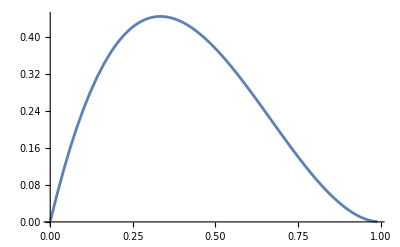

```mathematica
Plot[highESymmFunctional1[[1,1]]/.d->5,{x,1/1000,99/100},WorkingPrecision->50]
```

```mathematica
(*plot rep=1, J=20 functional vs x*)
```

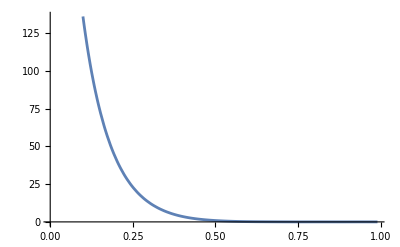

```mathematica
Plot[highESymmFunctional1[[1,10]]/.d->5,{x,1/1000,99/100},WorkingPrecision->50]
```

```mathematica
(*plot rep=1 impact param functional vs b*)
```

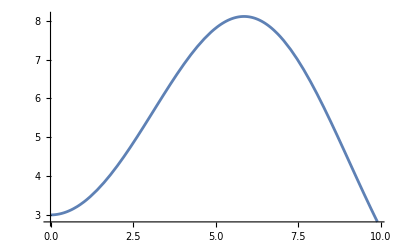

```mathematica
Plot[finiteImpParHighEFunctional1[[1]]/.d->5,{b,1/1000,99/10},WorkingPrecision->50]
```